## Bayesian Statistics, Exam 3

## Friday, Dec. 13, 2024 — Bayesian Conjugates and Monte Carlo Methods

## 1. A Beta Distribution Prior for Players Shooting 3-Pointers

An increasingly important shot in basketball is the “3-pointer.” In the NBA, this is a shot made from more than 23 feet 9 inches from the basket. There is a stripe on the court marking this distance.

Let’s say that an average offensive player that shoots 3-pointers succeeds 30% of the time. (Otherwise you might as well just go for 2-pointers, which offensive players can make about 45% of the time.)

The beta distribution formulas are:

P(x)=((x^(α-1)(1-x))^(β-1))/(B(α,β))

The mean of the beta distribution with parameters α and β is μ=α/(α+β).

 The variance of the distribution is σ^2=αβ/((α+β)^2(α+β+1)).

A. Let’s assume we have followed a bunch of players last season and their mean success rate μ=0.3. What combination of integers α and β will give μ=0.3? HINT: If you can’t just guess the combination of integers that works, try α=3 and see what β must be. I put in the hint :)

α= 3


β=


B. What does the variance come out to with the α and β you chose in Part A? Feel free to leave your answer for σ^2 as a rational fraction.


σ^2=


C. It turns out that the fraction you just calculated in B comes out to about σ^2=0.02 and taking the square root of that, you get a standard deviation, σ=0.14. On the plot below, draw three nice vertical lines at μ, at μ+σ, and at μ-σ. Shade in the region under the curve between these lines.

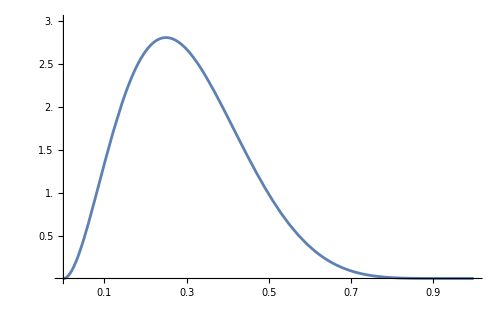

```mathematica
beta[x_]:=(x^(3-1)(1-x)^(7-1))/Beta[3, 7]
Plot[beta[x],{x,0,1}, PlotRange->{{0.0,1.0},{0.0,3.0}},Ticks->{Range[0.1,1.0,0.1],Range[0.5,3.0,0.5]}]
```

D. Make an estimate of the width, the average height, and the area of the region you have shaded in.


width = 


estimate of average height = 


estimate of area =


E. Convert your answer to D into an estimate of the percentage of players that make 3-pointers between 16% and 34% of the time.



F. To finish off your analysis of the prior, write it out with the α and β you have chosen (I’m just asking you to plug in and simplify as much as you can, and I know you aren’t going to be able to do anything to simplify the denominator):


prior(x)=((x^(α-1)(1-x))^(β-1))/(B(α,β))=


G. Oh, what the heck, I’ll make Mathematica simplify the denominator. Mathematica says the denominator is 1/252, and dividing by 1/252 is the same as multiplying by 252, so use that to write the prior again:


prior(x)=

## 2. A Likelihood for Nikola Jokic

Five days ago, on Dec. 8, Nikola Jokic of the Denver Nuggets made 3 out of 6 of the 3-pointers that he attempted against the Atlanta Hawks.

The formula for the binomial distribution with N attempts and n successes is

L(x)=(N
n)(x^n(1-x))^(N-n)

You don’t know x! It is whatever Nikola Jokic’s true success rate is, and you don’t know that from just one game’s data, so just leave x as a variable. Simplify L(x) as much as you can:


L(x)=


When you are simplifying you should use that

(N
n)=(N!)/((N-n)!n!)

Now you have a likelihood.

## 3. A Posterior for Nikola Jokic

A. Take the product of the prior from Problem 1 and the likelihood from Problem 2. Simplify it as much as you can, but note that the denominator is a nasty integral, so just leave it as “nasty integral” in your answer:

posterior(x)=(prior(x)*L(x))/(∫_0^1 prior(x)*L(x)ⅆx)=(prior(x)*L(x))/(nasty integral)=





B. Rewrite the posterior, but leaving all the constants off including “nasty integral” which is some constant that Mathematica could compute. All that is left is powers of x and 1-x. Write out what is left:


posterior(x)∝


C. This is your posterior, and you recognize that it is another beta distribution! What are the α and β of the posterior distribution?



D. Using your new α and β that describe the posterior, what is the average of the posterior distribution:

μ=α/(α+β)=

You can leave it as a rational fraction.

E. What is the variance of the posterior distribution:

σ^2=αβ/((α+β)^2(α+β+1))=

You can leave the variance as a rational fraction too.

COMMENT: The posterior is your new belief about Nikola Jokic’s 3-pointer success rate. After incorporating the Dec. 8 game, you could update your fantasy basketball software to reflect your new belief, and you could repeat the entire process the posterior becoming the prior before the next game.

## 4. Metropolis-Hastings Acceptance Ratios

In this problem, I am just going to have you show me that you understand the Metropolis-Hastings acceptance ratio. We’re going to do iPhone sales again, so there are four bins, numbered 1 to 4, for Q1, Q2, Q3, and Q4. Here are going to be our proposal probabilities, g(j|i):

g(2|1)=1.0

g(1|2)=0.5
g(3|2)=0.5

g(2|3)=0.5
g(4|3)=0.5

g(3|4)=1.0

This is pleasantly simpler than the Metropolis-Hastings example we did together, just because there are fewer possible proposals. 

Notice that:

* You can only propose moving right one bin from bin 1
* You have an equal chance of proposing left and right from either bin 2 or bin 3.
* Finally, you can only propose moving left one bin from bin 4.

We’ll use the same p's as in prior iPhone sales examples:

p_1=0.1
p_2=0.2
p_3=0.4
p_4=0.3

The formula for accepting a movement in Metropolis-Hastings is

min(p_j/p_i(g(i|j))/(g(j|i)),1).

On the next page, to two decimal places, compute the six acceptance probabilities.

NOTE: If you want any partial credit for wrong answers, write out the formula as I have done for the first one, so I have some chance of seeing what you did wrong.
 
accepting Q1->Q2:min(p_2/p_1(g(1|2))/(g(2|1)),1)= 

accepting Q2->Q1:

accepting Q2->Q3:

 
accepting Q3->Q2:

accepting Q3->Q4:

 
accepting Q4-> Q3:

## 5. Metropolis-Hastings Applied

If you are in bin 1, there is only one possible proposed move. You don’t need to flip a coin to choose the proposed move. Ditto for bin 4. So IF YOU ARE IN BIN 1 OR BIN 4, YOU CAN IGNORE THE COIN COLUMN. However, for bins 2 and 3, you have to flip a coin to decide which direction you go. SO THAT WE ARE ALL DOING THE SAME THING, a 0 in the coin column means propose to go left, and a 1 means propose to go right.

TO RANDOMLY DECIDE THE STARTING BIN, count the number of letters in your first name. If that is more than 4, subtract 4. There are only four possibilities. Maybe in my solution I will do all four. EXAMPLE: “Brian” has 5 letters. 5 is more than 4, so I subtract 4 and get 1. I start in bin 1.

```mathematica
smallIterations=10;
xxxrandomReals=Round[RandomReal[{0,1},smallIterations],0.01];
xxxrandomCoinTosses=RandomInteger[{0,1},smallIterations];
rounds=Range[1,smallIterations];
blanks = ConstantArray["                  ",smallIterations];
TableForm[Transpose[{rounds,blanks, randomCoinTosses, blanks, randomReals, blanks}], TableHeadings->{{},{"round", "current bin", "coin", "proposed bin","random", "result bin"}}]
```

| round | current bin | coin | proposed bin | random | result bin
 | 1 |                    | 0 |                    | 0.26 |                   
 | 2 |                    | 1 |                    | 0.62 |                   
 | 3 |                    | 1 |                    | 0.07 |                   
 | 4 |                    | 0 |                    | 0.66 |                   
 | 5 |                    | 0 |                    | 0.52 |                   
 | 6 |                    | 0 |                    | 0.96 |                   
 | 7 |                    | 1 |                    | 0.95 |                   
 | 8 |                    | 1 |                    | 0.54 |                   
 | 9 |                    | 0 |                    | 0.02 |                   
 | 10 |                    | 1 |                    | 0.76 |

## 6. Gibbs Sampling — Conditional Probabilities

The fine print is motivation. Read it if you want to understand where Gibbs sampling comes from. Or just skip the fine print and move to the actual problem.

=== BEGIN FINE PRINT ===
Gibbs sampling comes from statistical mechanics. Statistical mechanics explains things like how a gas can be on the verge of condensation. Let’s do the simplest statistical mechanics problem I can come up with that gives a hint of how statistical mechanics works.

Imagine a single atom stuck in a tall cylinder. Let’s say it can be the near the bottom of the cylinder, near the middle of the cylinder, or the near top of the cylinder and due to gravity, the bottom of the cylinder is the most probable place to find the atom:

p_bottom= 0.5
p_middle= 0.3
p_top= 0.2

Now we add a second atom that can also be near bottom, the middle or the top. So accounting for both of the atoms, there are now nine possibilities:

p_(1bottom 2bottom)=0.5 * 0.5 = 0.25
p_(1bottom 2middle)= 0.5 * 0.3 = 0.15
p_(1bottom 2top)= 0.5 * 0.2 = 0.10

p_(1middle 2bottom)=0.3 * 0.5 = 0.15
p_(1middle 2middle)= 0.3 * 0.3 = 0.09
p_(1middle 2top)= 0.3 * 0.2 = 0.06

p_(1top 2bottom)=0.2 * 0.5 = 0.10
p_(1top 2middle)= 0.2 * 0.3 = 0.06
p_(1top 2top)= 0.2 * 0.2 = 0.04

Now we add one more ingredient to start to mock up condensation. We make it a little more probable that the atoms want to be in the same region of the cylinder. In other words, we boost the probabilities of bottom-bottom, middle-middle, and top-top a little. Of course, to keep all the probabilities adding up to 1.00, we have to reduce the others a little.
=== END FINE PRINT ===

Whether or not you skipped the fine print, here are the 3x3=9 probabilities:

p_(1bottom 2bottom)=0.35
p_(1bottom 2middle)= 0.10
p_(1bottom 2top)= 0.05

p_(1middle 2bottom)= 0.10
p_(1middle 2middle)= 0.15
p_(1middle 2top)= 0.05

p_(1top 2bottom)= 0.05
p_(1top 2middle) = 0.05
p_(1top 2top) = 0.10

Now we’ll start computing conditional probabilities. Let’s say you are at a step in the algorithm where atom 1 and atom 2 are both in the middle state. Let’s say you are moving atom 2 only. So atom 1 remains in middle. Write down the three conditional probabilities for the movement of atom 2:


p_(1middle 2bottom |1middle)=


p_(1middle 2middle |1middle)=


p_(1middle 2top |1middle)=


HINT: Stuck on what to write down? You know the first conditional probability above has to somehow be proportional to p_(1middle 2bottom), so it must look like

(p_(1middle 2bottom))/denominator

Similarly, the second one must look like

(p_(1middle 2middle))/denominator

And the third one must look like

(p_(1middle 2top))/denominator

Finally, the denominator has to be such that all three of these conditional probabilities add up to 1.00.

## 7. Two-Dimensional Gibbs Sampling — Proposed Move

Now you draw a number between 0 and 1 to decide which of the three moves you make.

NOTE: I am going to put the ranges for Problem 7 on the blackboard.

Let’s say the number is 0.80. What is the proposed move:

_______________________________

## 8. Gibbs Sampling — More Conditional Probabilities

In Gibbs sampling, you always accept the proposed move. (And we proved that that works!). So now the algorithm is in the state you found in Problem 7. Now we move along the other axis. That means we move atom 1 only and 2 is fixed. What are the three conditional probabilities for atom 1:

p_(1bottom 2top |2top)=

p_(1middle 2top |2top)=

p_(1top 2top |2top)=

## 9. Gibbs Sampling — Another Proposed Move

Now you draw another number between 0 and 1 to decide which of the three moves you make.

NOTE: I will also put the ranges for Problem 9 on the blackboard.

Let’s say the number is 0.30. What is the proposed move:

_______________________________

## Name ______________________________________

1.              / 3
2.              / 3
3.              / 4
4.              / 5
5.              / 3
6.              / 3
7.              / 4
8.              / 5
9.              / 3

TOTAL          / 15